# Vierkant: Dichtheid en Absorptie

## LCA

```mathematica
Clear["Global`*"]
L = 1;
W = 1;
n = 25;
Ω = 1/Sqrt[2 Pi];


eigval[lijst_] := ((lijst[[1]] Pi)/L)^2+((lijst[[2]]  Pi)/W)^2
λlist = Part[SortBy[Tuples[Range[0,n],2], eigval[#]&],1;;n];
eigvals = Table[((Part[Part[λlist,i],1] Pi)/L)^2+((Part[Part[λlist,i],2] Pi)/W)^2, {i, 1, n}];
f[λ_, x_,y_] := Sqrt[2/L]Cos[(Part[λ,1] π)/L(x-L/2)] Sqrt[2/W]Cos[(Part[λ,2] π)/W(y-W/2)] /; Part[λ,1] ≠ 0 && Part[λ,2]≠ 0;
f[λ_, x_,y_] := Sqrt[1/(L W)] /; Part[λ,1] == 0 && Part[λ,2]== 0;
f[λ_, x_,y_] := Sqrt[2/(L W) ] (Cos[(Part[λ,1]  π)/L(x-L/2)] )/; Part[λ,1] ≠ 0 && Part[λ,2]==  0;
f[λ_, x_,y_] := Sqrt[2/(L W)] (Cos[(Part[λ,2]  π)/W(y-W/2)]  )/; Part[λ,1] == 0 && Part[λ,2]≠ 0;

Table[Plot3D[f[Part[λlist,i],x,y], {x,-L/2,L/2},{y,-W/2,W/2}, PlotLabel->StringForm["λ = ``", N[Re[Sqrt[Part[eigvals,i]]]]], AxesLabel->{Text[Style["x",FontSize->12]],Text[Style["y",FontSize->12]], Text[Style["Φ",FontSize->12]]}],{i,1,n}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Coulomb

```mathematica
Pm = Table[KroneckerDelta[i,j]   (((Part[Part[λlist,i],1] Pi)/L)^2+((Part[Part[λlist,i],2] Pi)/W)^2), {i, 1, n}, {j,1,n}];
Lm = ParallelTable[Ω^2  NIntegrate[(f[Part[λlist,i], x1,y1]  f[Part[λlist,j], x2,y2])/Sqrt[(x1-x2)^2+(y1-y2)^2 + (0.0001)^2],{x1,-L/2,L/2}, {y1,-W/2,W/2},{x2,-L/2,L/2}, {y2,-W/2,W/2},PrecisionGoal->6,AccuracyGoal->6,Method->{"GlobalAdaptive","MaxErrorIncreases"->5000},MinRecursion->30,MaxRecursion->100, WorkingPrecision->15],{i,1,n}, {j,1,n}];
Eigenvalues[Pm . Lm]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.01672038038612 and 0.104365368864387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000343874753914528 and 0.0843990543230543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000113924449994996 and 0.0896992433164921 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.239121465357771 and 0.0910413884359846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000819259029520461 and 0.0716789040659657 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00251248736330164 and 0.0720041143773051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000182738648459969 and 0.0712274212238211 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0292760977681904 and 0.0684042536404261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000343874753914528 and 0.0843990543230543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000107143690613478 and 0.0651350320554409 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00251248736330164 and 0.0720041143773051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000253348670344809 and 0.0760203977492168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000429237243233632 and 0.0845588311662215 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000162799409044104 and 0.0753406421596989 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000265509095300539 and 0.0624019639106283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000115065223269043 and 0.0605491086015408 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000029393744079977 and 0.0597679162544863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.25868521585611 and 0.0820118688696388 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.109415790010114 and 0.0758092771715611 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000248833401932887 and 0.0716789040659657 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000024587867295524367040381870718918195330866893446181924888907113801 and 0.056479509713251599722072439085376206899091751872721153464759424551 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.12702912892759 and 0.0727310229669156 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00010885847081126 and 0.0604828235831232 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0142325102243111 and 0.0604832862199273 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.083886165078552675057212592968738474031122909991770074693290232415 and 0.00013144705001796127169602491466736354840940415894960779419610726894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.2218567522547092604209988365343378817896456942263390773843361197×10^-8 and 0.000077712020444896684444508321231706845249978828989112520249561740243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000840785478474701 and 0.067875206611399 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.2218567522547092604209988365343378817896456942263390748982357053×10^-8 and 0.000077755938628002359826277082114620021058149939905683838179881628019 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00011629656336809098450754637752998351712224695164998660611833305065 and 0.072757524306056182502317326263002305633686905378566649886826154721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00019733788961957894133410863387237693486388240021546694977674425333 and 0.060910119896047884442163871992272359004426899669860264447649392396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.054866988488738677350489263581200983498201468033371624637960394725 and 0.000065567135114696705381660762537213041106576320087026816949333819109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000036356470758034262295227422769874865446767751031811787138543652201 and 0.062593755415163895683018901920954260419051926124760257004459656962 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0096825877498112097963729972370375979766199331520032000803031848269 and 0.000076121843593405288138693009209138457577396033316140150193511928188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000059192976784725349184321546714067837097885004856728821361713337396 and 0.052554028877309809052819889659442875266849689256746976881908695055 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000463422089196469 and 0.0915816825537689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.6086874713789541564920576360237047264058190354476338627427985585×10^-8 and 0.21759327756783167098067638793904741246660296184331786881116972816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0096825281383472438985650325883552030502381111922714631870009676092 and 0.000076911554848425651737496019565157798428205939983735486976771038568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0500092684474042 and 0.0761594402206337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.778927097822971382662398561396740791539730323670886043066673515×10^-8 and 0.000078123967951995545099539923935883752417884064374605477760477395939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.28699847253818×10^-6 and 0.0781120949651023 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.5689667312236027660013695352428115830458823579153812061156305149×10^-9 and 0.000072049231670259159903010085481644250325877256340947504472613383597 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.568966731229421808761324832656772264989851850671999987783869506×10^-9 and 0.000072049231670268143400723327432142493925000752991175297466618681627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.4683695247107929348408261179497556306353200636074656846824014344×10^-9 and 0.22413555647116210986842553993914769477134221652344209305159287631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000695593435547165 and 0.0553777027145949 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0065426551998109628027076973012389635578354015653780910398506053855 and 0.000063771675320482037433363243909297508578078465679002414188575677488 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.5453348644072137139109447575031662882522032787753843017197790009×10^-8 and 0.000076926259513265195611637271353230946376796003194896175190132551363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0065426398129125908918299210689993364750488786161252784012604761505 and 0.000063771675320480137977485854966302454839994164297335615343990797335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 5000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000014774410860218655501131946208104242237419222781677039783205741921 and 0.055268797435098342073437977058306891798733851517611334135895382884 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{44.2038884707874,36.7385901332259,31.5708028079021,28.88491136148,15.8350268887466,15.7005010265088,13.9083288425182,13.2455148619189,12.1808226595258,11.5821682879198,10.661525151198,10.5968350827922,8.41327426300384,8.36298397596149,8.3371231355587,8.23980463249953,7.72766022153433,5.31105043141418,5.27467006717965,4.98502234666428,4.94997720351424,2.67040044237239,1.87792345662218,1.85485483123437,0}

```mathematica
matrix = ToExpression[Import["C:\\Users\\frede\\Documents\\Wolfram Mathematica\\Thesis\\data\\VierkantLmPmN25Sqrt2Pi11jan.csv"]];
Plot3D[Evaluate@Table[(Sqrt[NIntegrate[-(D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{y,2}] + D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{x,2}])Sum[Eigenvectors[matrix][[j]][[i]] f[λlist[[i]],x,y]  , {i,1,n}],{y,-0.5,0.5},{x,-0.5,0.5}]])^-1(D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{y,2}] + D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{x,2}]),{j,n-1,n-1}],{x,-0.5 L,0.5 L},{y,-0.5,0.5}, PlotLegends->{"m=3","m=2","m=1"}, AxesLabel->Automatic,PlotRange->All]
Plot3D[Evaluate@Table[(Sqrt[NIntegrate[-(D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{y,2}] + D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{x,2}])Sum[Eigenvectors[matrix][[j]][[i]] f[λlist[[i]],x,y]  , {i,1,n}],{y,-0.5,0.5},{x,-0.5,0.5}]])^-1(D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{y,2}] + D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{x,2}]),{j,n-2,n-2}],{x,-0.5 L,0.5 L},{y,-0.5,0.5}, PlotLegends->{"m=3","m=2","m=1"}, AxesLabel->Automatic,PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
.
```

```mathematica
Export["VierkantLmPmN25Sqrt2Pi11jan.csv", matrix, "CSV"]
```

VierkantLmPmN25Sqrt2Pi11jan.csv

```mathematica
matrix = ToExpression[Import["VierkantLmPmN25Sqrt2Pi11jan.csv"]];
```

## Absorptie

```mathematica
α= Monitor[Table[NIntegrate[y (Sqrt[NIntegrate[(D[1/(Eigenvalues[matrix][[m]])Sum[Eigenvectors[matrix][[m]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{y,2}] + D[1/(Eigenvalues[matrix][[m]])Sum[Eigenvectors[matrix][[m]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{x,2}])Sum[Eigenvectors[matrix][[m]][[i]] f[λlist[[i]],x,y]  , {i,1,n}],{y,-0.5,0.5},{x,-0.5,0.5}]])^-1(D[1/(Eigenvalues[matrix][[m]])Sum[Eigenvectors[matrix][[m]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{y,2}] + D[1/(Eigenvalues[matrix][[m]])Sum[Eigenvectors[matrix][[m]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{x,2}]), {x,-0.5,0.5},{y,-0.5,0.5}],{m,1,n-1}],m]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.-5.81857×10^-8 ⅈ and 7.6442×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.+9.80812×10^-8 ⅈ and 2.15114×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.+9.52726×10^-8 ⅈ and 2.05066×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{0.-5.81857×10^-8 ⅈ,0.+9.80812×10^-8 ⅈ,0.+9.52726×10^-8 ⅈ,0.+3.48546×10^-9 ⅈ,0.+0.0387461 ⅈ,0.-0.0206097 ⅈ,0.-0.0000197285 ⅈ,0.+0.0000702119 ⅈ,0.-0.000145803 ⅈ,0.+0.00302379 ⅈ,0.+0.000967474 ⅈ,0.-0.029493 ⅈ,0.-0.000137651 ⅈ,0.-0.000188083 ⅈ,0.-0.00254656 ⅈ,0.-0.0885079 ⅈ,0.-0.000308334 ⅈ,0.+0.000564967 ⅈ,0.-0.0203917 ⅈ,0.-0.00112369 ⅈ,0.-0.000255043 ⅈ,0.+0.0000470366 ⅈ,0.-0.0512553 ⅈ,0.-0.527651 ⅈ}

```mathematica
αx= Monitor[Table[NIntegrate[x (Sqrt[NIntegrate[(D[1/(Eigenvalues[matrix][[m]])Sum[Eigenvectors[matrix][[m]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{y,2}] + D[1/(Eigenvalues[matrix][[m]])Sum[Eigenvectors[matrix][[m]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{x,2}])Sum[Eigenvectors[matrix][[m]][[i]] f[λlist[[i]],x,y]  , {i,1,n}],{y,-0.5,0.5},{x,-0.5,0.5}]])^-1(D[1/(Eigenvalues[matrix][[m]])Sum[Eigenvectors[matrix][[m]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{y,2}] + D[1/(Eigenvalues[matrix][[m]])Sum[Eigenvectors[matrix][[m]][[i]] f[λlist[[i]],x,y] , {i,1,n}],{x,2}]), {x,-0.5,0.5},{y,-0.5,0.5}],{m,1,n-1}],m]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.+1.73276×10^-7 ⅈ and 7.71365×10^-13 for the integral and error estimates.

{0.+0.000289139 ⅈ,0.+1.73276×10^-7 ⅈ,0.+0.0000423959 ⅈ,0.+2.50357×10^-6 ⅈ,0.-4.66694×10^-6 ⅈ,0.-5.56489×10^-6 ⅈ,0.-2.16271×10^-6 ⅈ,0.+0.0000212569 ⅈ,0.+0.000028157 ⅈ,0.+0.0000195504 ⅈ,0.-0.0237524 ⅈ,0.-0.000699211 ⅈ,0.-0.00187063 ⅈ,0.-0.0876891 ⅈ,0.+0.00953245 ⅈ,0.-0.000619855 ⅈ,0.-0.000241411 ⅈ,0.+0.0139209 ⅈ,0.-0.000167825 ⅈ,0.+0.0000866514 ⅈ,0.-0.0000784129 ⅈ,0.+9.90917×10^-6 ⅈ,0.+0.575597 ⅈ,0.+0.00497778 ⅈ}

```mathematica
Ω2 = 2.78*10^13* (1)^(1/4)/(√(2.75*0.02))
A[ω_] = Sum[(ω^2 Abs[α[[i]]]^2 Eigenvalues[matrix][[i]])/((ω^2 - Ω2^2 Eigenvalues[matrix][[i]])^2 + 0.3^2  Ω2^2  ω^2), {i,1,n-1}] ;
Ax[ω_] = Sum[(ω^2 Abs[αx[[i]]]^2 Eigenvalues[matrix][[i]])/((ω^2 - Ω2^2 Eigenvalues[matrix][[i]])^2 + 0.3^2  Ω2^2  ω^2), {i,1,n-1}] ;
```

1.1854×10^14

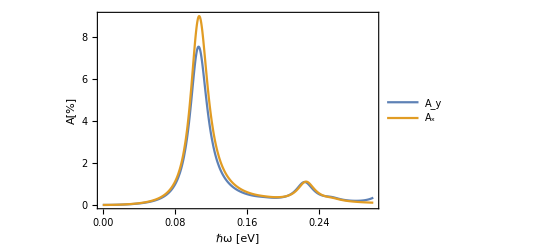

```mathematica
Plot[{(2(2.78*10^13)^2 *0.3 Ω2)/(3*10^12)A[ω*(6.58)^-1*10^16],(2(2.78*10^13)^2 *0.3 Ω2)/(3*10^12)Ax[ω*(6.58)^-1*10^16]}, {ω,0,0.3}, PlotRange->All,Frame->True,FrameLabel->{{Style["A_[%]", FontSize->16],""},{Style["ℏω [eV]", FontSize->16],""}},PlotLegends->{"A_y","A_x"}]
```